## Задание 1.

Спроектируйте и создайте функции для построения выпуклой оболочки заданного множества точек плоскости с использованием алгоритма Джарвиса . Проведите тестирование .

```mathematica
ClearAll[NamedQ,𝔨𝔪];
(** Атрибуты и описание **)
𝔨𝔪::usage="Knowledge base «computer mathematics»";
SetAttributes[𝔨𝔪,{Protected,ReadProtected}];
NamedQ::usage="Check: is there a name of tested equations";
NamedQ[n1_,n2__]:=And[NamedQ[n1],NamedQ[n2]];
SetAttributes[NamedQ,Listable];
```

```mathematica
ClearAll[kmPoint];
(** Атрибуты и описание **)
SetAttributes[kmPoint,ReadProtected];
kmPoint::usage="Point on the surface";
(** Свойства **)
NamedQ[kmPoint[𝔨𝔪,id_String,___]]^:=id≠"";
kmPoint[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmPoint[𝔨𝔪,id_String,___]["id"]:=If[id=="","Point",id];
(** Конструкторы **)
kmPoint[id_String,coord:{_,_}]:=kmPoint[𝔨𝔪,id,coord];
kmPoint[coord:{_,_}]:=kmPoint[𝔨𝔪,"",coord];
kmPoint[{L1_kmLine,L2_kmLine}]:=kmPoint[#[[2]]&/@(First@NSolve@Through[{L1,L2}@"equ"])]
(** Декораторы **)
Format[P_kmPoint,StandardForm]:=Row@{P["id"],"(",Row[P["coord"],","],")"};
```

```mathematica
ClearAll[kmVector];
(** Атрибуты и описание **)
SetAttributes[kmVector,ReadProtected];
kmVector::usage="Vector on the surface";
(** Свойства **)
NamedQ[kmVector[𝔨𝔪,id_String,___]]^:=id≠"";
kmVector[𝔨𝔪,id_String,___]["id"]:=If[id=="","Vector",id];
kmVector[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmVector[𝔨𝔪,_String,coord_List,___]["norm"]:=Sqrt[Plus@@(coord*coord)];
(** Конструкторы **)
kmVector[id_String,coord_List]:=kmVector[𝔨𝔪,id,coord];
kmVector[coord_List]:=kmVector[𝔨𝔪,"",coord];
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1@"coord"-P0@"coord"];
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
MakeBoxes[V_kmVector,StandardForm]^:=TemplateBox[{V@"id",
RowBox@Riffle[MakeBoxes[#,StandardForm]&/@V["coord"],","]
},"Point2D",
DisplayFunction:>(RowBox@{OverscriptBox[#1,"⇀"],"(",#2,")"}&),
InterpretationFunction->(RowBox@{"{",#2,"}"}&),
Tooltip->Automatic];
```

```mathematica
ClearAll[kmLine];
(** Атрибуты и описание **)
SetAttributes[kmLine,ReadProtected];
kmLine::usage="Line on the surface";
(** Свойства **)
NamedQ[kmLine[𝔨𝔪,id_String,___]]^:=id≠"";
kmLine[𝔨𝔪,id_String,___]["id"]:=If[id=="","Line",id];
kmLine[𝔨𝔪,_String,coef_List,___]["coef"]:=coef;
kmLine[𝔨𝔪,_String,coef_List,___]["equ",vars:{_Symbol,_Symbol}:{x,y}]:=
coef.Append[vars,1]==0;
(** Конструкторы **)
kmLine[equ:(__==0),vars:{_Symbol,_Symbol}]:=kmLine["",equ,vars];
kmLine[id_String,A_. x_+B_.y_+C_.==0,{x_Symbol,y_Symbol}]:=kmLine[𝔨𝔪,id,{A,B,C}]/;¬PossibleZeroQ[Abs@A+Abs@B];
kmLine[id_String,A_. x_+C_.==0,{x_Symbol,_Symbol}]:=kmLine[𝔨𝔪,id,{A,0,C}];
kmLine[id_String,B_. y_+C_.==0,{_Symbol,y_Symbol}]:=kmLine[𝔨𝔪,id,{0,B,C}];
kmLine[id_String,P_kmPoint,Dir_kmVector]:=kmLine[𝔨𝔪,id,
Append[#,-#.P["coord"]]&[({{0, -1}, {1, 0}}).Dir["coord"]]];
kmLine[P_kmPoint,Dir_kmVector]:=kmLine[
If[NamedQ[P,Dir],StringJoin[P@"id",Dir@"id"],""],P,Dir];
kmLine[id_String,P1_kmPoint,P2_kmPoint]:=kmLine[id,P1,kmVector["",P1,P2]]
kmLine[{P1_kmPoint,P2_kmPoint}]:=kmLine[P1,kmVector[P2@"id",P1,P2]]
kmLine[id_String,segment_kmSegment]:=Block[{x1=(segment["end1Coord"])["coord"][[1]],y1=(segment["end1Coord"])["coord"][[2]],x2=(segment["end2Coord"])["coord"][[1]],y2=(segment["end2Coord"])["coord"][[2]]},kmLine[id,(y1-y2)x+(x2-x1)y+(x1*y2-x2*y1)==0,{x,y}]]
kmLine[segment_kmSegment]:=Block[{x1=(segment["end1Coord"])["coord"][[1]],y1=(segment["end1Coord"])["coord"][[2]],x2=(segment["end2Coord"])["coord"][[1]],y2=(segment["end2Coord"])["coord"][[2]]},kmLine[(y1-y2)x+(x2-x1)y+(x1*y2-x2*y1)==0,{x,y}]]
(** Декораторы **)
Format[L_kmLine,StandardForm]:=Row@{L@"id",": ",L@"equ"};
```

```mathematica
ClearAll[kmSegment];
(** Атрибуты и описание **)
SetAttributes[kmSegment,ReadProtected];
kmLine::usage="Отрезок на плоскости";
(** Свойства **)
NamedQ[kmSegment[𝔨𝔪,id_String,___]]^:=id≠"";
kmSegment[𝔨𝔪,id_String,___]["id"]:=If[id=="","Segment",id];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["coords"]:=kmPoint[#]&/@endCoords;
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["end1Coord"]:=Module[{x1=endCoords[[1,1]],y1=endCoords[[1,2]],x2=endCoords[[2,1]],y2=endCoords[[2,2]]},If[x1<x2||y1<y2,kmPoint[{x1,y1}],kmPoint[{x2,y2}]]];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["end2Coord"]:=Module[{x1=endCoords[[1,1]],y1=endCoords[[1,2]],x2=endCoords[[2,1]],y2=endCoords[[2,2]]},If[x1<x2||y1<y2,kmPoint[{x2,y2}],kmPoint[{x1,y1}]]];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["len"]:=Sqrt[Plus@@((endCoords[[1]]-endCoords[[2]])^2)]
(** Конструкторы **)
kmSegment[id_String,endsCoords:{{_,_},{_,_}}]:=kmSegment[𝔨𝔪,id,endsCoords];
kmSegment[endsCoords:{{_,_},{_,_}}]:=kmSegment[𝔨𝔪,"",endsCoords];
kmSegment[id_String,P0_kmPoint,P1_kmPoint]:=kmSegment[id,{P1@"coord",P0@"coord"}];
kmSegment[P0_kmPoint,P1_kmPoint]:=kmSegment[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
Format[Segment_kmSegment,StandardForm]:=Row@{Segment@"id",": ",Segment@"coords"};
(**Отображение отрезка на рисунке**)
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[
ReplaceAll[gp,{
P_kmPoint:>Tooltip[Point@P@"coord",Style[Format[P,StandardForm],Large]],
L_kmLine:>Tooltip[
InfiniteLine@Through@getTwoLinePoints[L]@"coord",
Style[Format[L,StandardForm],Large]],
Segment_kmSegment:>Tooltip[Line[{Segment@"end1Coord",Segment@"end2Coord"}]]
}],
opts];
```

```mathematica
Q=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,3.45086-9.18317),Point(,,2.858025.56732),Point(,,-0.252913-7.45123),Point(,,6.30562.11851),Point(,,-5.67136.28036),Point(,,6.61471-2.6382),Point(,,1.111628.22183),Point(,,2.502244.22168),Point(,,-7.02371-5.97973),Point(,,-4.25387-6.94357),Point(,,7.837979.812),Point(,,6.10184-1.59721),Point(,,8.52569-7.70895),Point(,,9.01032-2.48938),Point(,,-7.379989.53141),Point(,,8.674195.42707),Point(,,3.704713.08658),Point(,,-3.644582.03114),Point(,,2.07225-1.91754),Point(,,6.094186.42131)}

```mathematica
getTriangleAlgebraicSquare[points_List]:=Module[{a=points[[1]]["coord"],b=points[[2]]["coord"],c=points[[3]]["coord"]},1/2 Det[{b-a,c-a}]]
```

```mathematica
isPointOnLine[Line_kmLine,P_kmPoint]:=Line["equ"]/.{x->P["coord"][[1]],y->P["coord"][[2]]}
```

```mathematica
Unprotect[Unequal];
```

```mathematica
Unequal[Point1_kmPoint,Point2_kmPoint]:=Point1["coord"]!=Point2["coord"]
```

Важно закинуть стартовую точку в конец Q.

```mathematica
getStartPoint[Q_List]:=Module[{StartPoint=Q[[1]]},
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<=StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
];
Return@StartPoint
]
```

```mathematica
moveToEndOfList[lst_List,obj_]:=Append[DeleteCases[lst,obj],obj]
```

```mathematica
getParameter[Segment_kmSegment,P_kmPoint]:=Block[{x0=Segment["end1Coord"]["coord"][[1]],x1=Segment["end2Coord"]["coord"][[1]],
y0=Segment["end1Coord"]["coord"][[2]],y1=Segment["end2Coord"]["coord"][[2]]},
If[x1-x0==0,(First@First@NSolve[(y1-y0)*t+y0==P["coord"][[2]],t])[[2]],(First@First@NSolve[(x1-x0)*t+x0==P["coord"][[1]],t])[[2]]]]
```

```mathematica
CH[pointsList_List]:=Module[{i=1,Q=pointsList,StartPoint,CurrentPoint,NextPoint,algebraicSquare,L={}},
StartPoint=getStartPoint[Q];
L=AppendTo[L,StartPoint];
Q=moveToEndOfList[Q,StartPoint];
CurrentPoint=StartPoint;
NextPoint=Q[[1]];
While[NextPoint!=StartPoint,
Do[
If[
isPointOnLine[
kmLine[{CurrentPoint,NextPoint}],i
]
&&
kmSegment[CurrentPoint,i]["len"]>kmSegment[CurrentPoint,NextPoint]["len"],NextPoint=i,
algebraicSquare=getTriangleAlgebraicSquare[{CurrentPoint,i,NextPoint}];
If[algebraicSquare>0,NextPoint=i]
],
{i,DeleteCases[Q,NextPoint]}
];
Q=DeleteCases[Q,NextPoint];
L=AppendTo[L,NextPoint];
If[NextPoint==StartPoint,Return@L];
CurrentPoint=NextPoint;
NextPoint=Q[[1]]
];
]
```

Проверяю

```mathematica
Q1=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,-4.449635.14737),Point(,,3.38075-3.72555),Point(,,-3.06303-1.97663),Point(,,2.85916.7018),Point(,,1.60589-6.07245),Point(,,-8.530653.94222),Point(,,1.203295.60252),Point(,,-2.69811-2.32946),Point(,,5.006547.76012),Point(,,4.80649-2.70935),Point(,,-2.25752-6.75846),Point(,,-5.134943.92009),Point(,,-3.46663-9.08841),Point(,,6.581861.18801),Point(,,4.060899.59161),Point(,,6.53913-6.41746),Point(,,4.341163.72293),Point(,,5.366937.03762),Point(,,-1.41955-2.98283),Point(,,-9.89377-4.69594)}

```mathematica
res1=CH[Q1]
```

{Point(,,-9.89377-4.69594),Point(,,-3.46663-9.08841),Point(,,6.53913-6.41746),Point(,,6.581861.18801),Point(,,5.366937.03762),Point(,,5.006547.76012),Point(,,4.060899.59161),Point(,,-8.530653.94222),Point(,,-9.89377-4.69594)}

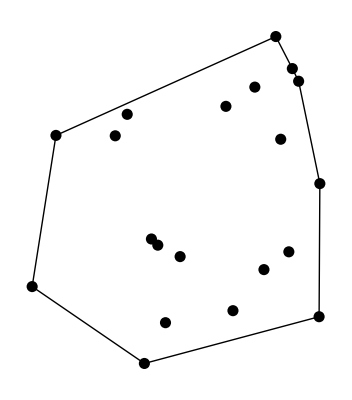

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q1,Line[{#["coord"]&/@res1}]}]
```

```mathematica
Q2={kmPoint[{6,3}],kmPoint[{6,5}],kmPoint[{3,5}],kmPoint[{6,1}],kmPoint[{1,2}],kmPoint[{1,1}],kmPoint[{3,1}],kmPoint[{4,6}],kmPoint[{2,4}],kmPoint[{6,5}],kmPoint[{5,1}],kmPoint[{1,3}]}
```

{Point(,,63),Point(,,65),Point(,,35),Point(,,61),Point(,,12),Point(,,11),Point(,,31),Point(,,46),Point(,,24),Point(,,65),Point(,,51),Point(,,13)}

```mathematica
res2=CH[Q2]
```

{Point(,,11),Point(,,61),Point(,,65),Point(,,46),Point(,,13),Point(,,11)}

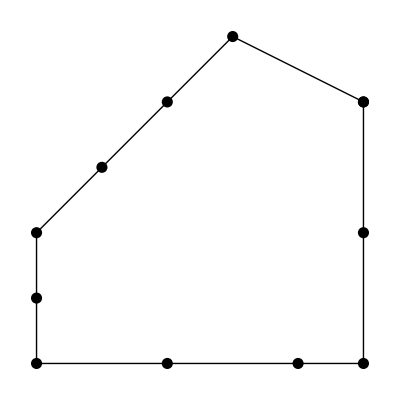

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q2,Line[{#["coord"]&/@res2}]}]
```